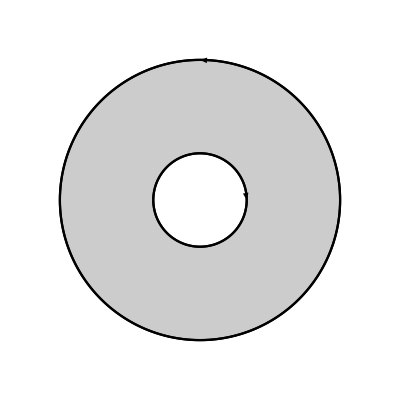

```mathematica
Quxian1=PolarPlot[1,{t,0,2Pi},PlotStyle->Black];
Quxian2=ParametricPlot[{3Cos[t],3Sin[t]},{t,0,2Pi},PlotStyle->Black];
Quyu=RegionPlot[x^2+y^2≥1^2&&x^2/3^2+y^2/3^2≤1,{x,-3.5,3.5},{y,-3.5,3.5},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100,AspectRatio->1];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0.001,2.99993},{0,3}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{0.999985,0.0001},{1,0}}]}];
Show[Quyu,Quxian1,Quxian2,g1,g2,AxesStyle->Arrowheads[0.04],Axes->Automatic,Frame->False,Ticks->None]
```

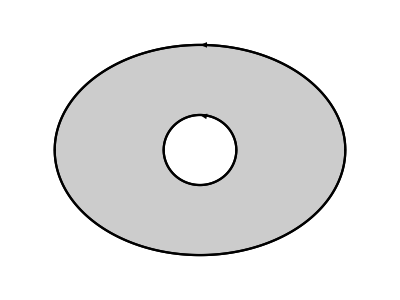

```mathematica
Quxian1=PolarPlot[1,{t,0,2Pi},PlotStyle->Black];
Quxian2=ParametricPlot[{4Cos[t],3Sin[t]},{t,0,2Pi},PlotStyle->Black];
Quyu=RegionPlot[x^2+y^2≥1^2&&x^2/4^2+y^2/3^2≤1,{x,-4.5,4.5},{y,-3.5,3.5},PlotStyle->GrayLevel[.8],BoundaryStyle->Black,PlotPoints->100,AspectRatio->3/4];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0.001,3},{0,3}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{0.0001,0.999978},{0,1}}]}];
Show[Quyu,Quxian1,Quxian2,g1,g2,AxesStyle->Arrowheads[0.04],Axes->Automatic,Frame->False,Ticks->None]
```

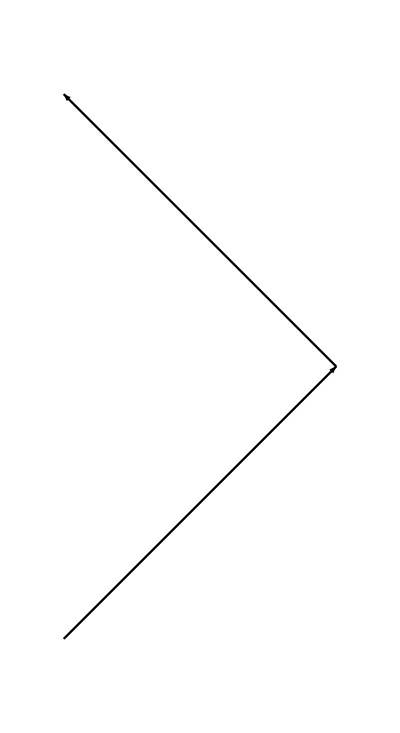

```mathematica
Quxian1=Plot[x-1,{x,0,1},PlotStyle->Black];
Quxian2=Plot[1-x,{x,1,0},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.08],Arrow[{{0,-1},{1,0}}]}];
g2=Graphics[{Arrowheads[0.08],Arrow[{{1,0},{0,1}}]}];
Show[Quxian1,Quxian2,g1,g2,PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesStyle->Arrowheads[0.07],Axes->Automatic,AspectRatio->2.2/1.2,Frame->False,Ticks->{{1},{-1,1}}]
```

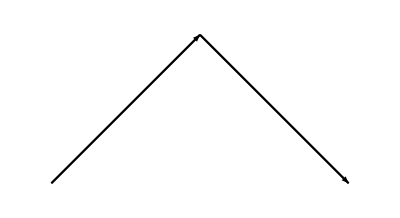

```mathematica
Quxian1=Plot[x,{x,0,1},PlotStyle->Black];
Quxian2=Plot[2-x,{x,1,2},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0,0},{1,1}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{1,1},{2,0}}]}];
Show[Quxian1,Quxian2,g1,g2,PlotRange->{{-0.1,2.1},{-0.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.2/2.2,Frame->False,Ticks->{{1,2},{1}}]
```

```mathematica
P1=Plot3D[{z=y},{x,-1.2,1.2},{y,-1.2,1.2},Axes->False, BoxRatios->{4,4,4},PlotStyle->{Green,Opacity[0.2]},Mesh->0,PlotPoints->100];
P2=ParametricPlot3D[{Sin[phi]*Cos[theta],Sin[phi]Sin[theta],Cos[phi]},{theta,0,2Pi},{phi,0,Pi},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Yellow,Opacity[0.3]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{Cos[theta],1/Sqrt[2]Sin[theta],1/Sqrt[2]Sin[theta]},{theta,0,2Pi},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Thickness[0.01],Red},Mesh->0,PlotPoints->100];
P4=ParametricPlot3D[{r Cos[theta],1/Sqrt[2]r Sin[theta],0},{theta,0,2Pi},{r,0,1},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Gray,Opacity[0.5]},Mesh->0,PlotPoints->100];
P5=ParametricPlot3D[{Cos[theta],1/Sqrt[2] Sin[theta],0},{theta,0,2Pi},Axes->False, BoxRatios->{1,1,1},PlotStyle->{Thickness[0.01],Gray},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Red,Arrowheads[0.05],Arrow[{{0.0001,Sqrt[2]/2-0.000015,Sqrt[2]/2-0.000015},{0,Sqrt[2]/2,Sqrt[2]/2}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[g1,G1,P1,P2,P3,P4,P5,ViewPoint->{-8,-4,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

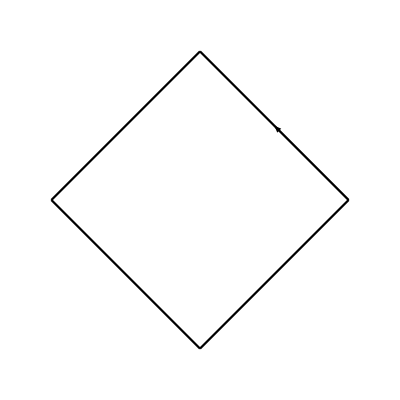

```mathematica
Quxian1=Plot[x-1,{x,0,1},PlotStyle->Black];
Quxian2=Plot[1-x,{x,1,0},PlotStyle->Black];
Quxian3=Plot[x+1,{x,0,-1},PlotStyle->Black];
Quxian4=Plot[-1-x,{x,-1,0},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0,-1},{1,0}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{1,0},{0.5,0.5}}]}];
g3=Graphics[{Arrowheads[0.05],Arrow[{{0,1},{-1,0}}]}];
g4=Graphics[{Arrowheads[0.05],Arrow[{{-1,0},{0,-1}}]}];
Show[Quxian1,Quxian2,Quxian3,Quxian4,g2,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->2.2/2.2,Frame->False,Ticks->{{-1,1},{-1,1}}]
```

```mathematica
P2=ParametricPlot3D[{Sin[phi]*Cos[theta],Sin[phi]Sin[theta],Cos[phi]},{theta,0,Pi/2},{phi,0,Pi/2},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Green,Opacity[0.3]},Mesh->0,PlotPoints->100];
P3=ParametricPlot3D[{Cos[theta],Sin[theta],0},{theta,0,Pi/2},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Thickness[0.01],Red},Mesh->0,PlotPoints->100];
P4=ParametricPlot3D[{Sin[phi]*Cos[0],0,Cos[phi]},{phi,0,Pi/2},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Thickness[0.01],Red},Mesh->0,PlotPoints->100];
P5=ParametricPlot3D[{0,Sin[phi],Cos[phi]},{phi,0,Pi/2},Axes->False, BoxRatios->{3,3,3},PlotStyle->{Thickness[0.01],Red},Mesh->0,PlotPoints->100];
g1=Graphics3D[{Red,Arrowheads[0.05],Arrow[{{0.001,0.999865,0},{0,1,0}}]}];
g2=Graphics3D[{Red,Arrowheads[0.05],Arrow[{{0,0.001,0.999865},{0,0,1}}]}];
g3=Graphics3D[{Red,Arrowheads[0.05],Arrow[{{0.999865,0,0.001},{1,0,0}}]}];
G1=Graphics3D[{{Black,Arrowheads[.03],Arrow[{{-1.5,0,0},{1.5,0,0}}]},{Black,Arrowheads[.03],Arrow[{{0,0,-1.5},{0,0,1.5}}]},{Black,Arrowheads[.03],Arrow[{{0,-1.5,0},{0,1.5,0}}]}},Axes->False,AxesOrigin->{0,0,0}];
Show[g1,g2,g3,G1,P2,P3,P4,P5,ViewPoint->{2,2,2},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

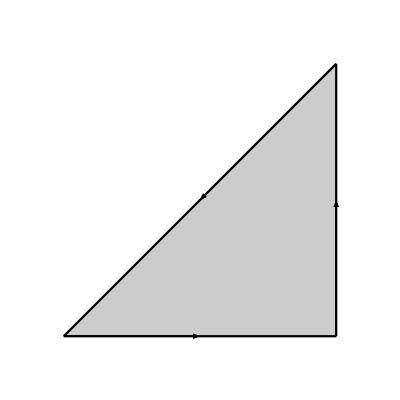

```mathematica
Quxian1=Plot[x,{x,0,1},Filling->Bottom,PlotStyle->Black];
Quxian2=ParametricPlot[{1,y},{y,0,1},PlotStyle->Black];
Quxian3=Plot[0,{x,0,1},PlotStyle->Black];

g1=Graphics[{Arrowheads[0.05],Arrow[{{1,0},{1,0.5}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{1,1},{0.5,0.5}}]}];
g3=Graphics[{Arrowheads[0.05],Arrow[{{0,0},{0.5,0}}]}];
Show[Quxian1,Quxian2,Quxian3,g1,g2,g3,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.2/1.2,Frame->False,Ticks->{{1,2},{1}}]
```

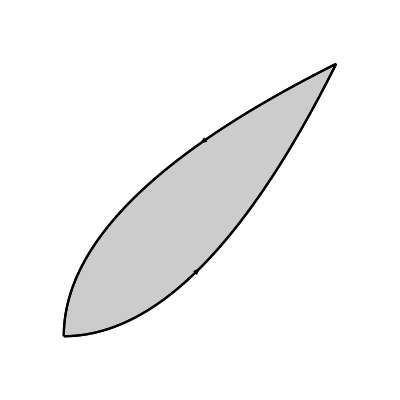

```mathematica
Quxian1=Plot[x^2,{x,-0,1.0},PlotStyle->Black];
Quxian2=ParametricPlot[{y^2,y},{y,0,1.0},PlotStyle->Black];
Region=Plot[{x^2,Sqrt[x]},{x,0,1},Filling->{2->{1}},PlotStyle->Black];

g1=Graphics[{Arrowheads[0.05],Arrow[{{0.5-0.0001,0.25-0.0001},{0.5,0.25}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{0.5,Sqrt[0.5]},{0.5-0.0001,Sqrt[0.5]-0.0001/2/Sqrt[0.5]}}]}];
Show[Quxian1,Quxian2,g1,g2,Region,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.2/1.2,Frame->False,Ticks->None]
```

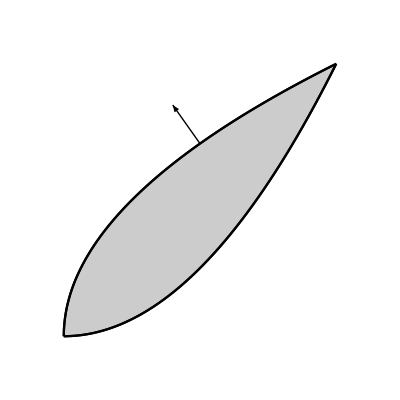

```mathematica
Quxian1=Plot[x^2,{x,-0,1.0},PlotStyle->Black];
Quxian2=ParametricPlot[{y^2,y},{y,0,1.0},PlotStyle->Black];
Region=Plot[{x^2,Sqrt[x]},{x,0,1},Filling->{2->{1}},PlotStyle->Black];

g1=Graphics[{Arrowheads[0.05],Arrow[{{0.5-0.0001,0.25-0.0001},{0.5,0.25}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{0.5,Sqrt[0.5]},{0.5,Sqrt[0.5]}+0.1{-1,2Sqrt[0.5]}}]}];
Show[Quxian1,Quxian2,g2,Region,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.2/1.2,Frame->False,Ticks->None]
```

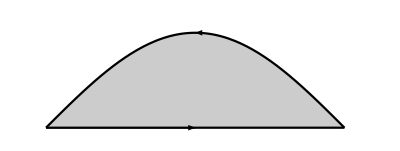

```mathematica
Quxian1=Plot[Sin[x],{x,-0,Pi},Filling->Bottom,PlotStyle->Black];
Quxian2=ParametricPlot[{x,0},{x,0,Pi},PlotStyle->Black];
g1=Graphics[{Arrowheads[0.05],Arrow[{{0,0},{0.5Pi,0}}]}];
g2=Graphics[{Arrowheads[0.05],Arrow[{{0.5Pi+0.001,1},{0.5Pi,1}}]}];
Show[Quxian1,Quxian2,g1,g2,PlotRange->{{-0.1,Pi+0.2},{-0.1,1.2}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1.3/(Pi+0.3),Frame->False,Ticks->{{Pi/2,Pi},{1}}]
```